```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/student/compphys/week9

```mathematica
data=ReadList["!./pdf 100000",Number];
```

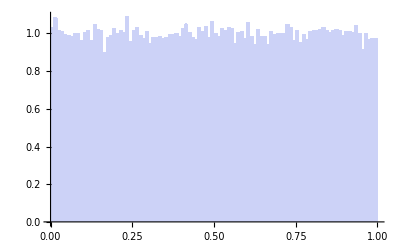

```mathematica
Histogram[data,100,"PDF"]
```

```mathematica
data=ReadList["!./pdf2 100000",Number];
```

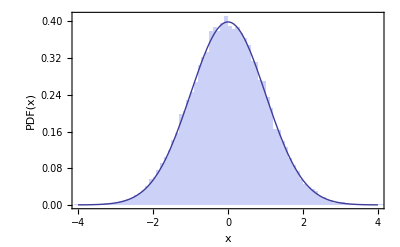

```mathematica
Show[Histogram[data,100,"PDF"],Plot[Exp[-x^2/2]/√(2π),{x,-4,4},PlotRange->All],Frame->True,PlotRange->{{-4,4},All},FrameLabel->{"x","PDF(x)"},BaseStyle->14]
```

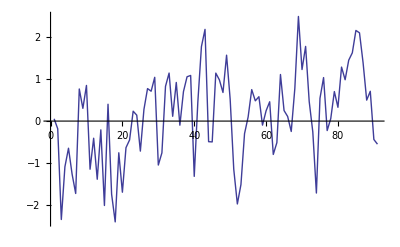

```mathematica
ListLinePlot[data[[100;;1000;;10]]]
```

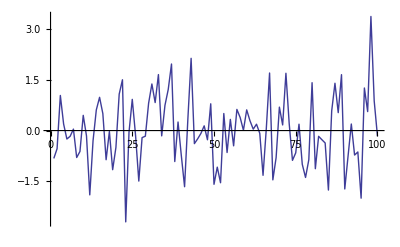

```mathematica
ListLinePlot[RandomVariate[NormalDistribution[],100]]
```

```mathematica
data=ReadList["!./pdf3 100000",Number];
```

```mathematica
zn=NIntegrate[Exp[-x^2/2]+Exp[-(x-8)^2/8],{x,-∞,∞}];
```

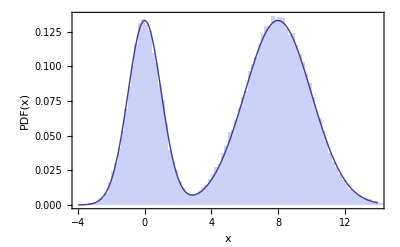

```mathematica
Show[Histogram[data,100,"PDF"],Plot[(Exp[-x^2/2]+Exp[-(x-8)^2/8])/zn,{x,-4,14},PlotRange->All],Frame->True,PlotRange->{{-4,14},All},FrameLabel->{"x","PDF(x)"},BaseStyle->14]
```

```mathematica
data=Partition[ReadList["!./gas 10 10 1 1 1 10000 10",Number],40];
```

```mathematica
data//Length
```

100

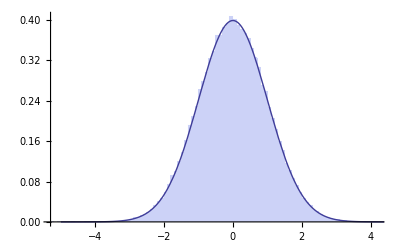

```mathematica
Show[Histogram[Flatten[data[[100;;,21;;]]],100,"PDF"],Plot[PDF[NormalDistribution[0,Sqrt[1.0]]][x],{x,-5,5}]]
```

```mathematica
ken[l_,n_]:=Total[l[[2n+1;;]]^2]/2
```

```mathematica
kendata=Table[ken[d,10],{d,data}]
```

{8.14179,14.1759,7.01571,«9995»,9.80666,7.28546}

```mathematica
Mean[kendata]
```

9.96556

```mathematica
StandardDeviation[kendata]/Sqrt[Length[kendata]]
```

0.0317668

```mathematica
bootstrap[list_,func_,tries_:100]:=Module[{meas},
meas=Table[func[RandomChoice[list,Length@list]],{tries}];
{Mean[meas],StandardDeviation[meas]}]
```

```mathematica
bootstrap[kendata,Mean]
```

{9.96861,0.0302783}

```mathematica
pot[l_,n_]:=Module[{v},
v[r_]:=4((1/r)^12-(1/r)^6);
Sum[v[Norm[l[[2*i-1;;2*i]]-l[[2*j-1;;2*j]]]],{i,n},{j,i+1,n}]]
```

```mathematica
potdata=Table[pot[d,10],{d,data}];
```

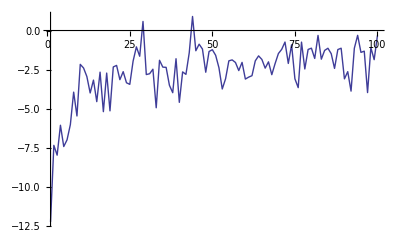

```mathematica
ListLinePlot[potdata[[;;100]],PlotRange->All]
```

```mathematica
show[l_,n_,L_]:=Graphics[{{FaceForm[],EdgeForm[Thick],Rectangle[{0,0},{L,L}]},{AbsolutePointSize[10],Table[Point[l[[2*i-1;;2*i]]],{i,n}]}}]
```

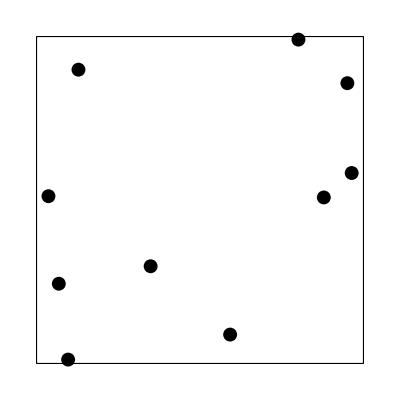

```mathematica
show[data[[1000]],10,10]
```